SimulationTools > ConvergenceTesting

# Convergence Testing

Many simulations involve the solution of partial differential equations using finite difference methods on a coordinate grid.  Several simulations, identical apart from the grid spacing, are then compared to see how the numerical solution changes with the grid spacing.  This is done both to show that the solution converges to an exact solution, and to assess the numerical error.

SimulationTools contains several functions to help in this process.

In the examples below, we will use a set of three DataTables constructed to simulate a second-order accurate numerical solution to some partial differential equation.

The grid spacings are

```mathematica
h1=1./10;h2=1./12;h3=1./20;
```

The “numerical solutions” are

```mathematica
f1=ToDataTable[Table[{t,Sin[2Pi t]+Cos[2Pi t]  h1^2},{t,0,1,h1}]]
```

DataTable[<11>,{{0.,1.}}]

```mathematica
f2=ToDataTable[Table[{t,Sin[2Pi t]+Cos[2Pi t] h2^2},{t,0,1,h2}]]
```

DataTable[<13>,{{0.,1.}}]

```mathematica
f3=ToDataTable[Table[{t,Sin[2Pi t]+Cos[2Pi t] h3^2},{t,0,1,h3}]]
```

DataTable[<21>,{{0.,1.}}]

We can plot the DataTables directly:

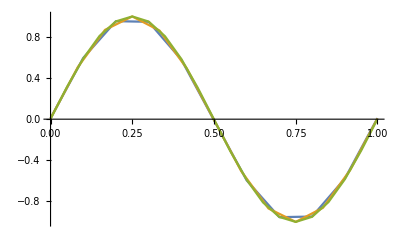

```mathematica
ListLinePlot[{f1,f2,f3}]
```

### Ratio between solution differences

Assuming convergence of the numerical solutions at a given order, the ratio between the differences of numerical solutions, f_1-f_2 and f_2-f_3 is given by

f_1-f_2=(f_2-f_3)× ConvergenceMultiplier[{h_1,h_2,h_3},p]+O(h^(p+1))

This is accurate to order p+1.

```mathematica
ConvergenceMultiplier[{h1,h2,h3},2]
```

0.6875

For the example above, we can confirm that the data satisfies this property by plotting the two differences, with the second one rescaled by the convergence multiplier:

```mathematica
cm=ConvergenceMultiplier[{h1,h2,h3},2]
```

0.6875

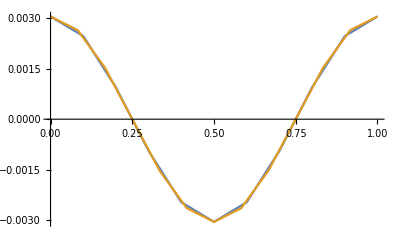

```mathematica
ListLinePlot[{f1-f2,(f2-f3)cm}]//WithResampling
```

The two curves lie on top of each other, since the convergence is exactly 2nd order in this case.

The WithResampling function is necessary in order for subtraction of DataTables on different coordinate grids to use interpolation automatically (the interpolation is 8th order by default).

### Convergence rate

You can also measure the convergence rate:

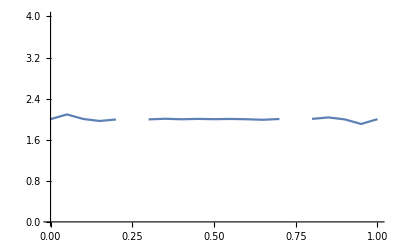

```mathematica
ListLinePlot[ConvergenceRate[{f1,f2,f3},{h1,h2,h3}],PlotRange->{0,4}]
```

Note that the convergence rate cannot be determined at the points where f_1-f_2=f_2-f_3

For general h_1, h_2 and h_3, the convergence rate cannot be solved for exactly; Mathematica’ FindRoot function is used to solve the algebraic equation.  As such, in certain cases a solution might not be found.

### RichardsonExtrapolant

Assuming a given order of convergence, you can use two of the solutions to estimate a higher-order approximation of the exact solution.  This is called Richardson Extrapolation and is useful for providing an error estimate in one of the numerical solutions.  The RichardsonExtrapolant function gives this estimate:

```mathematica
fExt=RichardsonExtrapolant[{f2,f3},{h2,h3},2]
```

DataTable[<21>,{{0.,1.}}]

An error estimate (accurate to 3rd order) for f3 can be determined by subtracting the Richardson extrapolant:

```mathematica
fErr=WithResampling[f3-fExt]
```

DataTable[<21>,{{0.,1.}}]

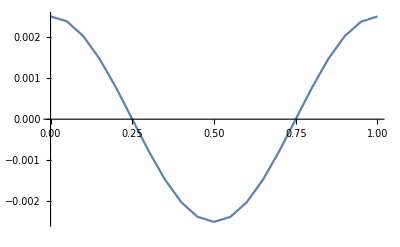

```mathematica
ListLinePlot[fErr]
```